```mathematica
f[μ_,x_]:= μ x (1-x)
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
```

```mathematica
Manipulate[ListPlot[fn[μ,0.4,#]&/@Range[100]],{μ,0,4}]
```

```mathematica
conf[μ_,n_]:=Length[Union[Round[ⅇ^μ(fn[μ,0.4,300+#]-fn[μ,0.4,300]),0.01]& /@Range[2^n]]]
```

```mathematica
data= ParallelTable[{μ,conf[μ,7]},{μ,2.8,3.5,10^-5}];
```

Ci metterebbe 12 anni a computarlo mi sa, io per sicurezza faccio npo a mano

#### Troviamo i punti a manina:

```mathematica
data0= ParallelTable[{μ,conf[μ,2]},{μ,2.8,3.1,10^-4}];
```

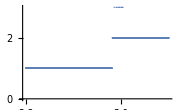

```mathematica
ListPlot[data0]
```

```mathematica
First@Last@Cases[data0,{_,1}]
```

2.9814

```mathematica
data1=ParallelTable[{μ,conf[μ,4]},{μ,3.1,3.5,10^-4}];
```

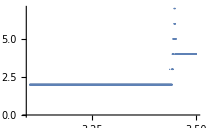

```mathematica
ListPlot[data1]
```

```mathematica
First@Last@Cases[data1,{_,2}]
```

3.4421

```mathematica
data2=ParallelTable[{μ,conf[μ,5]},{μ,3.443,3.6,10^-4}];
```

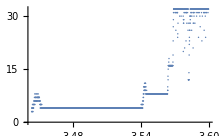

```mathematica
ListPlot[data2]
```

```mathematica
First@Last@Cases[data2,{_,4}]
```

3.5416

```mathematica
First@Last@Cases[data2,{_,8}]
```

3.5636

```mathematica
First@Last@Cases[data2,{_,16}]
```

3.5683

```mathematica
data3=ParallelTable[{μ,conf[μ,5]},{μ,3.56,3.58,10^-5}];
```

```mathematica
First@Last@Cases[data3,{_,16}]
```

3.57302

```mathematica
First@Last@Cases[data2,{_,32}]
```

3.6

#### da concludere

fare un data =Flatten[ {data_1,...,data_n}] o farlo computare un po’ con quella iniziale (o pi

```mathematica
μ[n_]:= First@Last@Cases[data,{_,2^n}]
```